```mathematica
ClearAll;
```

```mathematica
b=2;
```

```mathematica
odf=4*Sqrt[b/(2π)]*Exp[b*(Cos[2Θ]+1)]/Erfi[Sqrt[2*b]]
```

(4 ⅇ^(2 (1+Cos[2 Θ])))/(√π Erfi[2])

```mathematica
int=N[∫_0^π ∫_0^π odf*Sin[θ]ⅆθⅆΘ]
```

12.8653

```mathematica
ρip=1
```

1

```mathematica
rip=Join[Table[{Θ,odf/int},{Θ,-π/2,π/2,0.005}]];
```

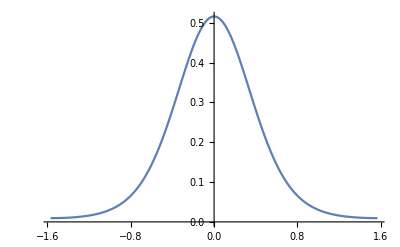

```mathematica
lp=ListPlot[{rip},Joined->True]
```

```mathematica
max=N[4*Sqrt[b/(2π)]*Exp[b*(Cos[2*0]+1)]/Erfi[Sqrt[2*b]]]
```

6.63701

```mathematica
N[Erfi[Sqrt[2*b]]]
```

18.5648

```mathematica
N[Exp[b*(Cos[2*0]+1)]]
```

54.5982

```mathematica
N[4*Sqrt[b/(2π)]]
```

2.25676

```mathematica
eval=N[Integrate[Interpolation[rip][x],{x,-Pi/2,Pi/2}]]
```

InterpolatingFunction::dmvali: The integration endpoint π/2 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.5

```mathematica
max/int
```

0.515885

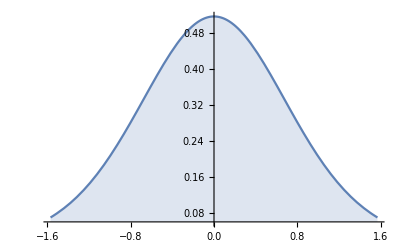

```mathematica
pvm=Plot[PDF[VonMisesDistribution[0,b],x]//Evaluate,{x,-Pi/2,Pi/2},PlotRange->All,Filling->Axis]
```

```mathematica
PDF[VonMisesDistribution[μ,κ],x]
```

Piecewise[{{ⅇ^(κ Cos[x-μ])/(2 π BesselI[0,κ]), -π+μ≤x≤π+μ}, {0, True}}]

```mathematica
ρop=N[4Sqrt[b/(2π)]*Exp[b*(Cos[2Θ]-1)]/Erf[Sqrt[2*b]]];
```

```mathematica
N[Erfi[Sqrt[2*b]]]
```

18.5648

```mathematica
Exp[3]-E^3
```

0

2

18.5648

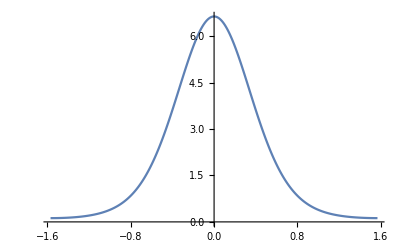

```mathematica
bb=Sqrt[2*b]
erfi=π^(-1/2)*(2*bb+2*bb^3/3+∑_(j=3)^60 bb^(2*j-1)/(0.5*(2*j-1)*Factorial[(j-1)]))
ρipee=N[4*Sqrt[b/(2π)]*Exp[b*(Cos[2*Θ]+1)]/erfi];
rippp=Join[Table[{Θ,ρipee},{Θ,-π/2,π/2,0.005}]];
lpee=ListPlot[{rippp},Joined->True]
```